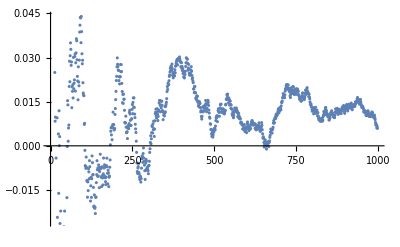

```mathematica
(* (a) Test the central limit theorem with square distribution *)
(* (b) Test convergence to mean with Normal distribution *)
(* (c) Test convergenve to mean with Levy distribution *)

NN=1000;
(* create list with NN random draws from Uniform Distribution *)
dataR=RandomVariate[UniformDistribution[{-1.0,+1.0}],NN];
(*create a list of lists: list with one element, list with two elements, list with three elements,... *)
dataRc=Table[Drop[dataR,-1*n],{n,1,NN-1}];
sum1={};
(* calculate mean of every list in lists and accumualte results in sum1 *)
For[j=1,j≤ NN-1,j++,AppendTo[sum1,Mean[dataRc[[NN-j]]]//N   ]];
(* Plot mean for every list in dataRc *)
ListPlot[sum1]
```

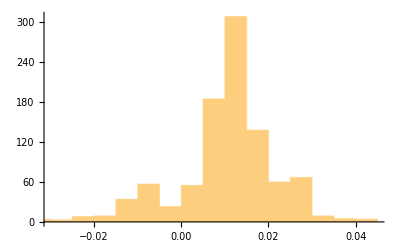

```mathematica
Histogram[sum1]
```

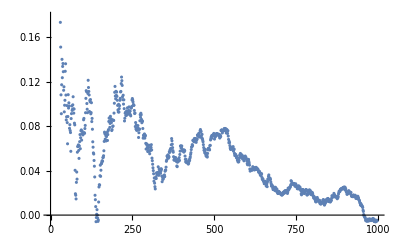

```mathematica
dataR=RandomVariate[NormalDistribution[0,1.0],NN];
dataRc=Table[Drop[dataR,-1*n],{n,1,NN-1}];
sum1={};
For[j=1,j≤ NN-1,j++,AppendTo[sum1,Mean[dataRc[[NN-j]]]//N   ]];

ListPlot[sum1]
```

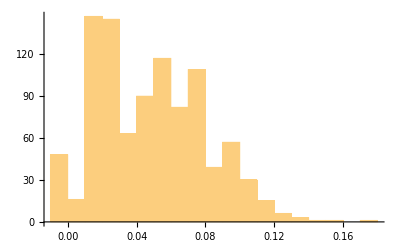

```mathematica
Histogram[sum1]
```

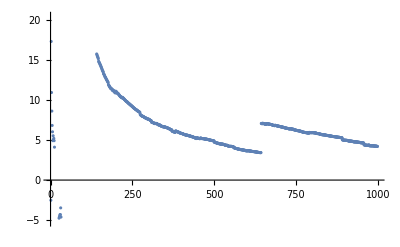

```mathematica
NN=1000;
dataS=RandomVariate[StableDistribution[1,1,0,0,1.5],NN];
dataSc=Table[Drop[dataS,-1*n],{n,1,NN-1}];
sum2={};
For[j=1,j≤ NN-1,j++,AppendTo[sum2,Mean[dataSc[[NN-j]]]//N   ]];

ListPlot[sum2]
```

```mathematica
(* repeat manually and observe response *)
R=RandomVariate[UniformDistribution[{-1.0,+1.0}],1000];
Mean[R]
R=RandomVariate[NormalDistribution[0,+1.0],1000];
Mean[R]
```

-0.0150256

0.0178069

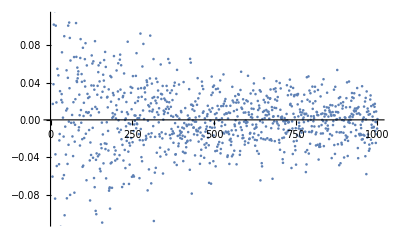

```mathematica
(* now let's do it with another approach *)
(* question: what is different here ? *)
dataSc=Table[Mean[RandomVariate[UniformDistribution[{-1.0,+1.0}],n]],{n,1,NN}];
ListPlot[dataSc]
```

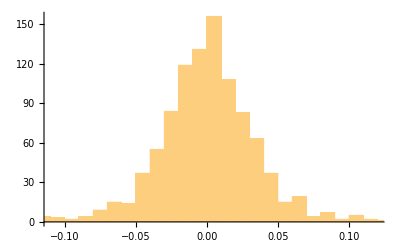

```mathematica
Histogram[dataSc]
```